# What is Going on in Biology? The Wolframian Perspective

## Willem Nielsen

What is the nature of biological processes? How do they look? What can they achieve? What happens when they go wrong?  These are such simple questions, and yet the field of biology, in my view, has largely failed to give people good answers. 

In my experience, modern academic institutions are really bad at answering big questions like this, and most of the best “scientists” of our time have found ways to make progress not because of these institutions but despite them. 

So okay these are bold statements, who do I think I am, right? Well, I think most biologists have largely missed a powerful new class of models: those based on simple computational rules. And because of this, they have been limited in their ability to give good high-level descriptions of what is going on in biology. 

For thirty years now, Stephen Wolfram has been filling this gap, and has pioneered some groundbreaking computational models for biological systems. Starting as a fan of the research, and eventually becoming a collaborator, I’ve become convinced that with Wolfram’s models, we’ve struck gold, and are now in a position to understand and communicate the high-level features of biology better than ever before. 

Despite this, most people outside of the Wolfram circle don’t know about his work in biology. So, myself and others at the Wolfram Institute thought it would be a good idea to bring all of Wolfram’s work in biology into one place, so that those who are curious can get up to speed as fast as possible. 

Stephen has published a ton of work that is very accessible, and I will link to it as we go.

But my goal with this article is to provide a single chronological and theoretical thread through his research in theoretical biology. Even by telling this story, I’ve felt my intuition for biology growing. Not only that, I’ve felt that understanding Stephen’s biological work in its entirety, has sparked ideas for interesting future directions of research in biology. And my hope, is that the reader will have a similar experience. 

Okay, so, where to start? The first important piece of the story is understanding Stephen himself, so who the hell is this guy? And what makes him special?

### Stephen’s Backstory

From my observations and interactions with Stephen at Wolfram Summer School and working with him on the medicine post, my impression is he was basically born to be a scientist. 

The one sentence summary is that he’s just an extremely curious, intelligent, friendly, and independent-minded person. This combination is very unique, and so it makes him a powerful force in the world of science and technology.

In addition to Stephen’s personality, I believe his story can also tell us a lot about what makes his research in biology different.

So what was that story? 

Well, he’s been doing serious science since he was a teenager. He famously got interested in the second law of thermodynamics from this textbook on the subject at the age of twelve:

```mathematica
-Graphics--Graphics-
```

The book, was unique from other physics books in that its conclusions did not require a trust in authority, rather one could “reach the truth” simply by understanding the ideas in the book.  In Stephen’s words “what was so exciting that day was that I got a first taste of the idea that one didn’t have to be told how the world works; one could just figure it out”:

This idea, that the arrangement of gas particles tends towards disorder, was also his first introduction to the “science of complexity” (although it didn’t have that name at the time) and importantly for us, it was this interest that would eventually lead him to model the origin of complexity in biological systems. This connection, was by no means a linear path though. 

He spent his teens and early twenties deep in the field of particle physics. While very far from biology, it was during this time that he figured out that computers could be useful for doing science, often using them to do physics calculations. And this appreciation for the computer as a tool for science would grow and become an essential theme in his future work, including, in biology.

In his words, Stephen “quickly outgrew” the computational tools he was using. And after getting his PhD in physics, he decided to work on building a software system that could, once-and-for-all, fulfill all his scientific needs. 

This famously turned into Mathematica, which ended up being extremely useful for Stephen (and others) in doing science. But more than being a useful tool, the process of building Mathematica continued to help develop Wolfram’s intuition that many of these “human creations” like mathematical equations, and the models of physics, could indeed be boiled down to computational rules.

With this powerful new tool and understanding, and with the rapid improvement of computers, Stephen began to separate himself from the traditions of physics, mostly using computational models instead of mathematical ones. 

But what did all this mean for his childhood interest in complexity? Well after having success with Mathematica by stripping things down to their computational essentials, he began to use the same approach in his scientific endeavors. In particular, he started developing a “minimal model for complexity”. 

After repeatedly refining and simplifying, he arrived at what he would call a 1-dimensional cellular automata, some early print-outs of these 1D automata are shown below:

And with these powerful new minimal models, he began to make significant progress in answering his long held questions about the origin of complexity.

The first step, was the formulation of the concept of “computational irreducibility”. In exploring the behavior  of cellular automata, he started to realize that “unpredictability” was actually quite common, and he began to speculate about what that could mean for science. Here is an amusing piece of a transcript from the conference where he first spoke publicly about computational irreducibility:

The next crucial step, came from Rule 30. Interestingly, Stephen had looked at Rule 30 two years earlier in 1982, but he hadn’t yet understood its importance. After more study of cellular automata and after printing it out in higher resolution, its significance hit him, and he realized, that surprisingly, complex phenomena can originate not just from complex programs but even from simple ones. Here we show the earlier low resolution printout of Rule 30 on the left and the higher resolution one on the right:

```mathematica
-Graphics--Graphics-
```

And seeing these two images side-by-side, you can see why the second one was what made things click. What rule 30 so beautifully shows, is that, starting from a simple initial condition (with one black cell) and running a simple set of rules (eight rules in this case) one can already generate complex, or random behavior.

Digressing slightly, this story also nicely illustrates how the accessibility of Stephen’s models played an important role in expediting his thinking.

I mentioned earlier that Wolfram was born to do science. But I also believe, that he was extremely lucky to find a path that enabled him to become well-versed in both the world of computation and the world of science. And it turned out, that there were a lot of low-hanging fruit in that intersection. 

In particular, nobody had captured the essence of complexity in such a simple model as in rule 30. And I think the fact that the model was so simple, gave him the mental clarity to realize its importance, and eventually connect the idea to so many different fields, as he did in New Kind of Science.

You might imagine that good ideas come from the mind, and the smartest minds have the best ideas. But even for someone as talented as Stephen, it was seeing the right picture that made all the difference in the formulation of his career-defining idea. 

And I’ve definitely experienced this phenomena in my own intellectual journey. Being able to readily visualize the behavior of cellular automata, I believe, has allowed me to understand things that I would’ve never understood otherwise, like the ubiquity of hierarchy in animals societies, or understanding why treating cancer is so difficult. Oddly enough, I can feel myself getting smarter by staring at looking at these computational creatures. 

Anyways, these two insights, computational irreducibility and the idea that simple programs can create complex behavior, were the seeds that grew into what would become New Kind of Science (NKS), where Stephen would make his first well-known foray into the field of theoretical biology.

### Biology in New Kind of Science

The connection to biology was quite straightforward (in retrospect at least); Given that simple programs could produce infinite complexity, Stephen speculated that much of the complex phenomena in biology was not a result of meticulous natural selection, but rather just a result of the fact that complexity was easy to generate.

One striking example he gives is in pigmentation patterns.

Pigmentation patterns of mollusk shells for example, in most species, are not exposed during the organisms lifetime and therefore have no effect on their fitness. But as you can see, from the array of shell images below, the patterns are very complex and look remarkably similar to the behavior of cellular automata.

-Graphics-

Here are some examples of similar cellular automata for comparison:

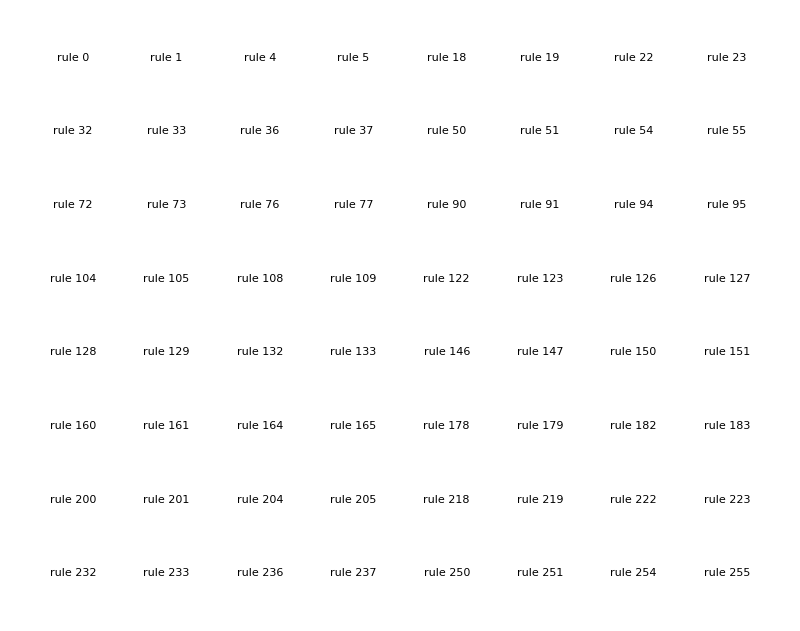

```mathematica
With[{srules=FromDigits[#,2]&/@Cases[Table[IntegerDigits[n,2,8],{n,0,255}],{_,a_,_,b_,a_,_,b_,_}],trand=BlockRandom[SeedRandom[12424,Method->"Legacy"];RandomInteger[1,50]]},GraphicsGrid[Partition[Labeled[RulePlot[CellularAutomaton[#],trand,30,PlotRangePadding->None,ImageSize->90],Text[Style["rule "<>IntegerString[#],Italic]]]&/@srules,8],ImageSize->800]]
```

So what this example makes obvious, is that behaviors in biological systems aren’t always the result of natural selection: because the pigmentation patterns aren’t visible during the mollusc’s lifetime, we know there is no way of selection acting on them. Clearly, the complexity comes simply as a side-effect of the system responsible for generating pigmentation. And in fact, just like a cellular automata, mollusk shells can only grow on their edge, or “one line at a time”, further suggesting that the biological patterns can indeed be modeled by these simple programs.

But okay, is this true for pigmentation in general, or just for mollusks? 

Looking at other branches in the tree of life, we can see that these automaton-like pigmentation patterns are not at all unique to molluscs:

And in fact, Stephen shows that one can imitate many of these pigmentation patterns using simple programs:

```mathematica
Layer[n_]:=Layer[n]=Select[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],MemberQ[#,n|-n]&]

Layer[n_,1]:=Layer[n,1]=Cases[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],{_,n|-n}]

Layer[n_,2]:=Layer[n,2]=Complement[Layer[n],Layer[n,1]]

SpotStep[w_List?VectorQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i]]Total[RotateLeft[list,#]&/@Layer[i]],{i,0,Length[w]-1}],{2}]

SpotStep[w_List?MatrixQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i,j]]Total[RotateLeft[list,#]&/@Layer[i,j]],{i,0,Length[w]-1},{j,2}],{2}]

SpotEvolveList[w_List,list_,n_]:=NestList[SpotStep[w,#]&,list,n]

GraphicsGrid[Table[MapIndexed[ArrayPlot[#1,FrameLabel->{None,Text[Style["step "<>Apply[IntegerString,#2],Italic]]}]&,SpotEvolveList[rule,BlockRandom[SeedRandom[12424,Method->"Legacy"];RandomInteger[1,{60,60}]],6]],{rule,{{1,1,-0.4,-0.4},{1,1,-0.2,-0.2}}}],ImageSize->700]
```

-Graphics-

```mathematica
Layer[n_]:=Layer[n]=Select[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],MemberQ[#,n|-n]&]

Layer[n_,1]:=Layer[n,1]=Cases[Flatten[Table[{i,j},{i,-n,n},{j,-n,n}],1],{_,n|-n}]

Layer[n_,2]:=Layer[n,2]=Complement[Layer[n],Layer[n,1]]

SpotStep[w_List?VectorQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i]]Total[RotateLeft[list,#]&/@Layer[i]],{i,0,Length[w]-1}],{2}]

SpotStep[w_List?MatrixQ,list_]:=Map[Boole[#>0]&,Sum[w[[1+i,j]]Total[RotateLeft[list,#]&/@Layer[i,j]],{i,0,Length[w]-1},{j,2}],{2}]

SpotEvolveList[w_List,list_,n_]:=NestList[SpotStep[w,#]&,list,n]

GraphicsGrid[Table[MapIndexed[ArrayPlot[#1,FrameLabel->{None,Text[Style["step "<>Apply[IntegerString,#2],Italic]]}]&,SpotEvolveList[rule,BlockRandom[SeedRandom[12424,Method->"Legacy"];RandomInteger[1,{60,60}]],6]],{rule,{{{1,1},{1,1},{-0.4,0},{-0.4,0}},{{1,1},{1,1},{0,-0.6},{0,-0.6}}}}],ImageSize->700]
```

-Graphics-

The above pictures show four evolutions of a 2D cellular automata. The first two rows use the same rule starting from slightly different random initial conditions. The second two rows use rules with different horizontal and vertical weights. The variation in the patterns here is remarkably similar to those we just saw in biology. This makes clear the idea that the variation observed in different pigmentation patterns can result from small changes to simple programs.

So okay, the complex pigmentation patterns in biology seem to be a side-effect of the simple programs that generate pigmentation.

But how do we know for sure that these complex pigmentation patterns aren’t a result of some careful evolutionary process?

To test this, Stephen looks at constraint satisfaction problems, in an attempt to evolve to some particular pattern. As an example we can try to reach the constraint that every black cell should have exactly one neighbor; The pattern shown below, together with its rotations and reflections, is the only one that satisfies this constraint:

```mathematica
CloudGet["https://wolfr.am/nks-page0211b-graphic"]
```

-Graphics-

The “evolution” starts with a random grid of cells, a single cell chosen randomly, is reversed, if that cell does satisfy the local-constraint, then that change is kept, if it doesn’t then it is “rejected”. Here we show a few successive changes that were kept:

```mathematica
ConstraintViolations[array_]:=Count[Partition[array,{3,3},1],{{_,a_,_},{b_,x_,c_},{_,d_,_}}/;!(a+b+c+d==If[x==1,1,2]),{2}];
```

```mathematica
SeedRandom[3060];
arrs = Gather[NestList[With[{new=MapAt[1-#&,#,RandomInteger[{1,10},2]]},If[ConstraintViolations[new]>ConstraintViolations[#],#,new]]&,RandomChoice[{1,0},{10,10}],1000]];
```

```mathematica
pos = SparseArray[#]["ExplicitPositions"]&/@ Subtract@@@Partition[arrs[[All, 1]], 2, 1];
```

```mathematica
reps = MapThread[ReplacePart[#1, Thread[#2->Red]]&, {arrs[[2;;,1]], pos}];
```

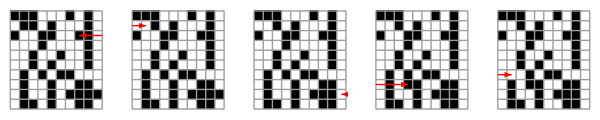

```mathematica
GraphicsRow[MapThread[{{"[◼]", "PerturbedArrayPlot"}}[#1, #2, "ArrowStyle"->Directive[Haloing[White],Arrowheads[.1]]]&,{arrs[[2;;6, 1]],pos[[;;5]]}], ImageSize->{600, Automatic}]
```

And here is our “loss curve”, or how many cells don’t satisfy the constraints:

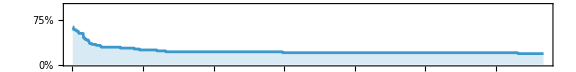

```mathematica
SeedRandom[3060];
ListLinePlot[ConstraintViolations/@NestList[With[{new=MapAt[1-#&,#,RandomInteger[{1,10},2]]},If[ConstraintViolations[new]>ConstraintViolations[#],#,new]]&,RandomChoice[{1,0},{10,10}],1000],Sequence[AspectRatio->1/8,PlotRange->{All,{0,65}},Filling->Axis,Frame->True,PlotRangePadding->0,ImageSize->Large,FrameTicks->{{Table[{n,Style[StringTemplate["``%"][100 (n/64)]]},{n,0,64,16}],False},{Automatic,False}}]]
```

So clearly we are making some progress towards satisfying the constraint, but how close do we get to the actual pattern?

Running this algorithm for many more steps and looking at snapshots along the way, we can see in the end the resulting pattern still doesn’t really look like the target pattern:

```mathematica
CloudGet["https://wolfr.am/nks-page0345a-graphic"]
```

-Graphics-

The problem, as Stephen explains, is that evolutionary algorithms tends to get stuck at local minima. Because the landscape for navigating these complex discrete systems is relatively rough, the algorithm will inevitably get stuck before it reaches some specific detailed pattern:

```mathematica
CloudGet["https://wolfr.am/nks-page0346b-graphic"]
```

-Graphics-

But can you get around this?

If you “relax the evolution”, by injecting some randomness into the search, Stephen finds that the iterative procedures end up with better results, but often only after an enormous amount of steps that would be infeasible for evolution.

And the takeaway here, is that evolution is limited in its ability to shape systems. This strongly suggests that the details of pigmentation patterns are not the result of some careful  evolutionary process, and their complexity is just a side-effect.

Now you may be thinking, “this pigmentation stuff is interesting, but what about other systems in biology?”

Well, one thing Stephen studies in NKS, is the shape of different organisms. In particular, he looks at the shapes of different leaves in the plant kingdom.

```mathematica
CloudGet["https://wolfr.am/nks-page0403a-graphic"]
```

-Graphics-

And what he finds is that the variation and complexity of leaf shape, can be also be modeled by changes to simple programs, in this case, substitution programs with slightly different branching radii:

```mathematica
GraphicsColumn[GraphicsRow[Flatten@{Graphics[{Line[#[[1]]],With[{head=#[[1,1,2]]},{Disk[head,.1],Arrowheads[.125,1.5],Arrow[{{head[[2]]-.4,head[[2]]},{head[[2]]+.4,head[[2]]}}]}],Translate[{Line[Flatten[#[[1;;2]],1]],Disk[#,.1]&/@#[[2,All,2]]},{2.5,0}]},Sequence[ImageSize->{Automatic,40},Frame->True,FrameTicks->False,FrameStyle->AbsoluteThickness[1],PlotRange->{{-0.75,3.4},{-0.25,2.25}}]]&@#[[4]],Graphics[{AbsoluteThickness[.3],Line/@#},Sequence[Frame->True,FrameTicks->False,PlotRange->All,PlotRangePadding->Scaled[0.05],FrameStyle->AbsoluteThickness[1]]]&/@#}&@With[{grow=#},Table[NestWhileList[Flatten[With[{head=#[[2]],dir=#[[2]]-#[[1]]},{head,head+#}&/@ReIm@grow[dir[[1]]+dir[[2]] I]]&/@#,1]&,{{{0,0},{0,1}}},(Length[#]<500&)],{θ,120 °,15 °,-15 °}]],ImageSize->{750,Automatic}]&/@Table[Function[Evaluate@Table[With[{t=θ ((2 i-2)/(Length[lengths]-1)-1)},# lengths[[i]] (Cos[t]+Sin[t] I)],{i,Length[lengths]}]],{lengths,{{.4,.7,.4},{.5,.4,.5},{.5,.5,.5},{.5,.6,.5},{.55,.8,.55},{.7,.8,.7},{.65,.6,.65},{.5,.6,.6,.5},{.65,.65}}}],ImageSize->Large]
```

-Graphics-

He then uses similar ideas to study animal growth and shape, in particular looking at the shapes of various shells. But the point is  that much like pigmentation, the observed variance and complexity in organism shape can mostly be explained not by natural selection, but rather by small changes in the underlying rules of simple programs.

To summarize the biological claims of NKS, we can imagine two views on biology. The first view, is that biological systems start as this simple goop. And evolution, is an adept and sober “sculptor”, meticulously removing bits of goop into these very specific shapes and patterns, that are chosen, because they are somehow more fit.

An alternative view, is that instead, biological systems, from the start are this complex amalgamation of parts that are capable of a wide range of different behaviors. And evolution is like a drunk, blindfolded sculptor, that is just doing its best to keep the biological systems from devolving into chaos.

In the first “sober sculptor model”, the causality lies with evolution, and the observed phenomena can be traced back to natural selection. In the second “drunk sculptor model”, the causality mostly lies with the systems, and biological phenomena can be explained mostly by modeling the physical systems.

Especially when New Kind of Science was published, the sober sculptor view was popular among biologists, and so Stephen made a point to emphasize the drunk sculptor view.

To be clear though, even in the drunk sculptor view, evolution does have some effect, and Stephen is not saying that it doesn’t. But the crucial point, is its effects will be high-level and the intricate details of biological systems can better be explained by computational irreducibility then by natural selection.

In NKS though, Stephen did not actually have a minimal model for the evolution of adaptive systems. He touched on it with the constraint satisfaction problems, but critically, this was only really modeling the process of pigmentation, and there was no clear picture of a “computational organism”.

In recent times, Stephen has made progress on this front, and it is the critical new element in his view on biology.

### Recent Work

Okay so what is his new work?

For a long time, as mentioned, he spent more of his efforts on the developmental side of biology, rather than the evolutionary side. In attending biology conferences he would often think about what is the space of all possible rules like, and in NKS, in the context of discussing evolution, he actually noted that nearby rules did seem to have similar behavior:

```mathematica
IdentityCARule[k_Integer,r_Integer]:=Flatten[Table[Table[Table[i,{j,k^r}],{i,k-1,0,-1}],{m,k^r}]]

EvolveCARuleStep[rule_List,k_Integer,r_Integer,newnonid_:1,changenonid_:1,newid_:1]:=Module[{newrule=rule,id,pos,set,center=IdentityCARule[k,r],rand=RandomReal[{0,newnonid+changenonid+newid}]},id=Flatten[Position[Drop[MapThread[Equal,{center,rule}],-1],TrueQ[rand<newnonid]]];
If[Length[id]>0,pos=id⟦RandomInteger[{1,Length[id]}]⟧;set=If[rand<newnonid+changenonid,Complement[Range[0,k-1],If[rand<newnonid,{rule⟦pos⟧},{rule⟦pos⟧,center⟦pos⟧}]],{center⟦pos⟧}];If[Length[set]>0,newrule⟦pos⟧=set⟦RandomInteger[{1,Length[set]}]⟧]];newrule]

EvolveCARule[k_Integer,r_Integer,count_Integer,newnonid_:1,changenonid_:1,newid_:1]:=NestList[EvolveCARuleStep[#,k,r,newnonid,changenonid,newid]&,IdentityCARule[k,r],count]

EvolveCARuleGraphic[rule_,k_,r_,colormap_:{GrayLevel[0.85],GrayLevel[0],GrayLevel[0.4]}]:=Module[{center=IdentityCARule[k,r]},Graphics[{Table[If[rule⟦i⟧==center⟦i⟧,{Black,Point[{i+.5,.5}]},{colormap⟦rule⟦i⟧+1⟧,Rectangle[{i,0},{i+1,1}]}],{i,k^2 r+1}],Line[{{1,0},{1,1},{Length[rule]+1,1},{Length[rule]+1,0},{1,0}}],Table[Line[{{i,0},{i,1}}],{i,2,Length[rule]}]},ImageSize->110]]

BlockRandom[SeedRandom[245671,Method->"Legacy"];
T=Take[First/@Split[EvolveCARule[3,1,200,1,1,0.1]],54]];

leg=EvolveCARuleGraphic[#,3,1]&/@T;

rp=RulePlot[CellularAutomaton[{FromDigits[#,3],3,1}],CenterArray[{1,2,1},65],30,ImageSize->110]&/@T;

GraphicsGrid[Partition[MapThread[Labeled[#1,#2,ImageSize->110]&,{rp,leg}],6],ImageSize->{650, Automatic}]
```

-Graphics-

But, he never really had the intuition or motivation to think that this was worth exploring further.

That changed when he started doing more work on machine learning, both practically for the development of Wolfram Language (Mathematica), and scientifically in understanding how ChatGPT works. And in one of his posts on machine learning, in trying to answer the question, “Can one find a system that does X?” he attempted to compare what a neural network could achieve with what a random iterative search could achieve. This, in combination with hearing about his friend Greg Chaitlin’s work relating the Busy Beaver problem to evolution, he was motivated to try out some adaptive algorithms on cellular automata. More specifically, he tried “evolving” a cellular automata, by changing one rule at a time, to find a pattern that had a particular finite length:

And to his surprise, it actually worked, here is an example evolution to length 50:

```mathematica
deathdiff[rule_,t_:100,max_:150]:=With[{array=CellularAutomaton[rule,{{1},0},{max,All}]},Abs[LengthWhile[Reverse[array],Total[#]==0&]-(max-t)]]
```

```mathematica
randrulesx[rule_,n_Integer,k_:5]:=FromDigits[#,k]&/@With[{dig=IntegerDigits[rule,k,k^3]},Union[Table[ReplacePart[dig,RandomInteger[{1,Length[dig]-1}]->RandomInteger[{0,k-1}]],n]]]
```

```mathematica
Grid[Partition[Framed[ArrayPlot[CellularAutomaton[#,{{1},0},{55,{-14,14}}],GridLines->{None,{5}},
GridLinesStyle->Directive[Thickness[.015],GrayLevel[0,.8]],ColorRules->{0->White,1->Hue[0.08, 1, 1],2->Hue[0.75, 0.86, 0.8200000000000001],3->Hue[0.14, 0.81, 0.99]},
Frame->None,ImageSize->59],FrameStyle->GrayLevel[0, 0.3],FrameMargins->0]&/@(SeedRandom[7067];With[{k=3},
NestList[{First[First[SortBy[{#,deathdiff[{#,k,1},50,100]}&/@randrulesx[#[[1]],100,k],Last]]],k,1}&,
{k RandomInteger[k^k^3/k],k,1},20]]),10],Spacings->{.25,.25}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

This simple idea then blossomed into a bunch of new work in theoretical biology from Stephen in early 2024. From this model of evolution, there were many interesting experiments to try, conclusions to be drawn, and implications for biology to share. Before I get to those though, I should be more precise about how the “adaptive evolution” works.

Starting from the null rule, you make a single random change (mutation) to one rule in the automaton. If that rule, with an initial condition of a single red square, leads to a longer or equal length pattern (that is the number of steps until it goes to white), then you keep that change. Here’s what it looks like when we show successive changes to the ruleset, or “genotype”, that were kept:

```mathematica
e3 = Module[
{deep=5000,cut=200,ru,life},
SeedRandom[5000+53];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]];
```

```mathematica
keptrus = First/@Split[First/@e3];
```

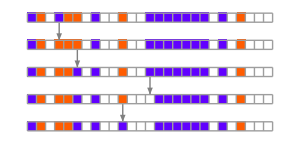
-Graphics-
⋮
-Graphics-
⋮

```mathematica
Column[{{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicates[keptrus][[1;;5]],(*"Arrows"->"Line",*)ImageSize->300],"⋮",{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicates[keptrus][[100;;104]],(*"Arrows"->"Line",*)ImageSize->300],"⋮"},Center]
```

And here is the “breakthrough phenotypes”, or steps in the evolution where a longer finite length (higher fitness) was achieved:

```mathematica
e3 = Module[
{deep=5000,cut=200,ru,life},
SeedRandom[5000+53];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]];
```

```mathematica
evo=Map[DeleteDuplicates,SplitBy[e3,Last]];
```

```mathematica
res=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,20(Length[data]+1)^.7},
Mesh->True,MeshStyle->Opacity[.1] ]]&,
evo,{2}];
```

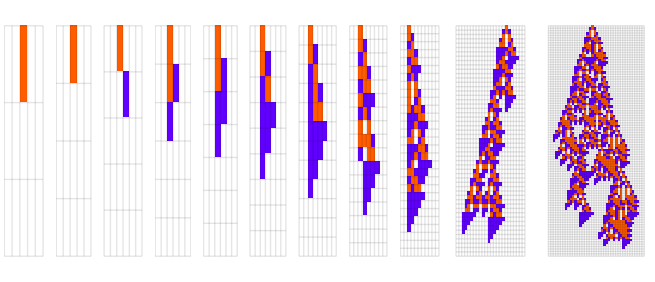

```mathematica
GraphicsRow[First/@res]
```

So already you can see the qualitative resemblance to biological evolution. 

And the thing that is most striking about these patterns is their sheer complexity. In other words, the mechanisms that the pattern uses to achieve the “goal” of increasing finite lifetime, are very intricate and therefore difficult to explain. Thus, in many cases, the best we can do in answering the question of why this particular pattern was “selected”, will be to say, “because it was”.

And in fact, running more evolutions, we see that in each case, very different underlying mechanisms are used, which suggests that most of the details of the pattern are not a result of the selection process, but rather just happened to have occurred in that particular evolutionary path:

```mathematica
es = Module[
{deep=5000,cut=200,ru,life},
SeedRandom[5000+#];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},0},deep]]&/@ {54, 60, 16};
```

```mathematica
evos=Map[DeleteDuplicates,SplitBy[#,Last]]&/@es;
```

```mathematica
ress=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,20(Length[data]+1)^.7} ]]&,
#,{2}]&/@ evos;
```

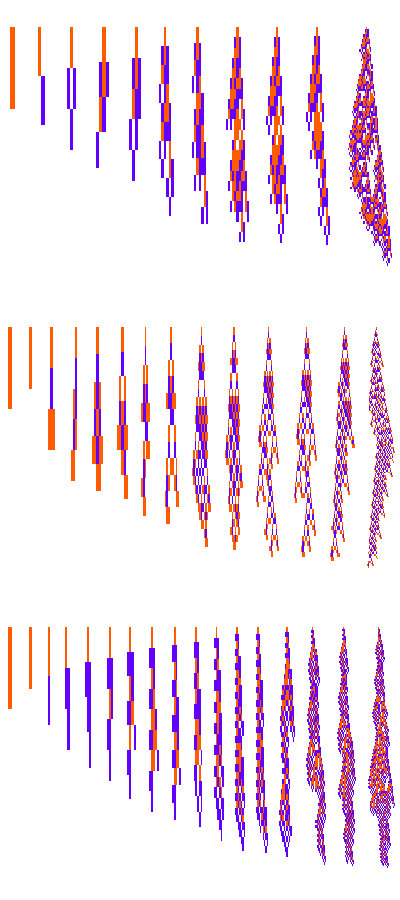

```mathematica
Column[GraphicsRow[First/@#]&/@ Prepend[ress[[;;-2]], ress[[-1]]]]
```

And Stephen shows that this is quite a general phenomena. Looking at different rule spaces, for example, we see more of the same, here is the k = 4, r = 1 case:

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
evos = Module[
{deep=2000,cut=200,ru,life,evo,data},
SeedRandom[426778+#];
evo=NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep]
]&/@ {181, 43};
```

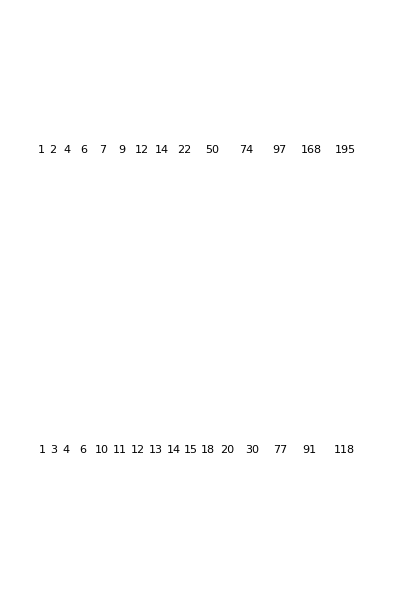

```mathematica
Column[GraphicsRow[Labeled[{{"[◼]", "PlotCA"}}[First[#],"Trim"->{1,5},ImageSize->{Automatic,22.5 Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@Rest[#[[ResourceFunction["ProgressiveMaxPositions"][#[[All,-1]]]]]]]&/@ evos]
```

Or the two-dimensional case, where we also see considerable complexity:

```mathematica
allrules=;
```

```mathematica
Row[Labeled[ArrayPlot3D[CellularAutomaton[<|"RuleNumber"->#[[1,1]],"Neighborhood"->9,"Dimension"->2,"Colors"->2|>,{CrossMatrix[1],0},#[[1,2]]],Method->{"ShrinkWrap"->True},ImageSize->{Automatic,22(#[[1,2]])^.5},Lighting->,ColorRules->{1->Hue[0.06, 0.93, 0.96]},Mesh->None],Text[Style[#[[1,2]]-1,Small]]]&/@allrules[[190]]]
```

-Graphics3D-0-Graphics3D-1-Graphics3D-3-Graphics3D-4-Graphics3D-6-Graphics3D-12-Graphics3D-14-Graphics3D-49-Graphics3D-93-Graphics3D-145-Graphics3D-147-Graphics3D-163-Graphics3D-166-Graphics3D-235

Or even with different fitness functions, here we’re selecting for wider patterns instead of longer:

```mathematica
Module[{
k=3,r=1,cut=800,deep=5000,fun=Length@*First,
init,evo,ru,data,lt,test,mask,canonical,res},
res=[[;;3]];
res=Map[CompoundExpression[
data=CellularAutomaton[{#[[1,1]],3,1},{{1},0},#[[2]]+2],
ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
ImageSize->{Automatic,Min[20(Length[data]+1)^.7,600]}]]&,
res,{2}];
GraphicsColumn[GraphicsGrid[{#}]&/@res,Automatic,0]
]
```

-Graphics-

Or aspect ratio, here are some results of searching for a pattern that has a 3:1 aspect ratio:

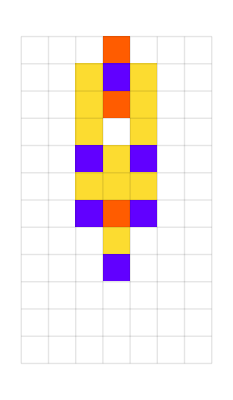
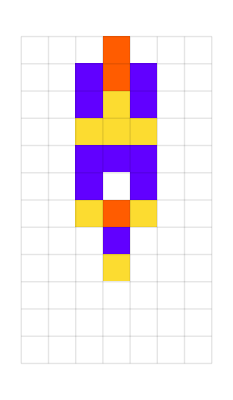
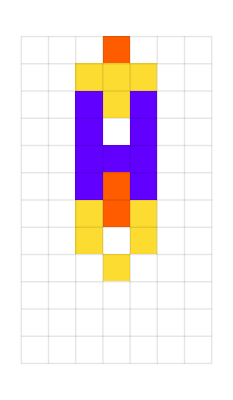
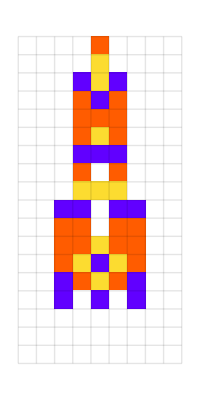
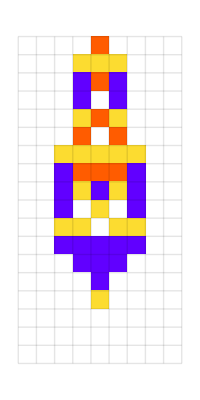
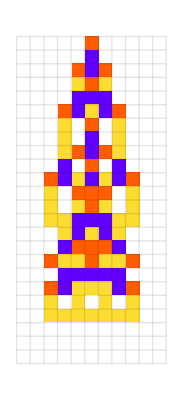
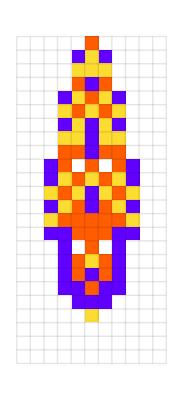
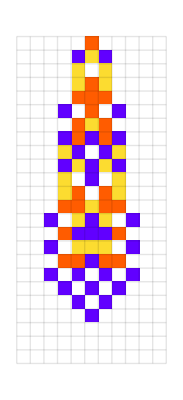
{-Graphics-{9,3},-Graphics-{9,3},-Graphics-{9,3},-Graphics-{15,5},-Graphics-{15,5},-Graphics-{21,7},-Graphics-{21,7},-Graphics-{21,7},-Graphics-{21,7},-Graphics-{21,7},-Graphics-{27,9},-Graphics-{27,9},-Graphics-{39,13},-Graphics-{45,15},-Graphics-{51,17},-Graphics-{57,19},-Graphics-{57,19},-Graphics-{69,23},-Graphics-{69,23},-Graphics-{111,37}}

```mathematica
Style[With[{data=CellularAutomaton[
#[[1]],{{1},0},#[[2,1]]+2]},
Labeled[ArrayPlot[ArrayPad[#,2]&/@data,
ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,24Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
],Style[#[[2]],"Text",Italic,Gray,11]]]&/@{{{109636419052937157723438118980837975564,4,1},{9,3}},{{232259557841861635493049224869714791688,4,1},{9,3}},{{338236923684700346441755364009144414988,4,1},{9,3}},{{3663450190864856052378894455912568704,4,1},{15,5}},{{136651796051772457646439217666630305548,4,1},{15,5}},{{74948306682547943335519680440646385168,4,1},{21,7}},{{193464179513193600562914906378802444040,4,1},{21,7}},{{193649253952380488246394671786963518216,4,1},{21,7}},{{298798483958213368517806363132769509688,4,1},{21,7}},{{337623673395850352619393223745807586160,4,1},{21,7}},{{143430394600545658197868087730119774096,4,1},{27,9}},{{246493520306698100424983701858655419148,4,1},{27,9}},{{180664442152675280322045408237394267792,4,1},{39,13}},{{36324902254124465598971313626629143056,4,1},{45,15}},{{289850694849104464885050820643032709680,4,1},{51,17}},{{143923012087109979886256736424975337072,4,1},{57,19}},{{280384207228392989942672757173339297804,4,1},{57,19}},{{283391784414472610606660051001734099568,4,1},{69,23}},{{330335253914559274144004959766636949128,4,1},{69,23}},{{142140648448642989785750794400464692296,4,1},{111,37}}},LineSpacing->{1.1,0}]
```

So the claim is that natural selection in biology works similarly to these cases in the sense that evolution selects organisms based on some high-level metric of fitness. But, because biological systems are capable of arbitrarily complex behavior (just like our automata), the processes used to satisfy the fitness functions will be full of irreducibility.

In Stephen’s language, evolution is like a computationally-bounded observer of computationally unbounded processes.

In NKS, Stephen had models for subsystems within biology, like pigmentation, growth and shape. And with these models he showed that much of the variation and complexity of these subsystems arose as a consequence of computational irreducibility.

With these new adapted cellular automata, he now has a generalized model for all biological processes, not just pigmentation, growth and shape. And with this more abstract model, he can provide a clearer picture for the behavior of biological processes in general.

And as we’ve seen, these pictures strongly suggest once again that the dominant force in biological systems is computational irreducibility and not natural selection.

Okay, so what else can we takeaway from this new model?

So far, we’ve been discussing the individual patterns, but what about the space of all possible patterns?

Well, we can actually draw a “fitness landscape” by showing the graph of all possible rules:

```mathematica
Module[{mg,lifetimes,g1,g2,emb,toRule,fromRule,lp3},
mg={{"[◼]", "MutationGraph"}}[2,3/2];
lifetimes=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2]][[2,1,1]];
g1=GridGraph[Table[2,15]];
emb=GraphEmbedding[g1];
g2=NearestNeighborGraph[Tuples[{1,0},15],
VertexCoordinates->Automatic];
toRule=Map[FromDigits[Append[#,0],2]&,
FindGraphIsomorphism[g1,g2][[1]]];
fromRule=Association[Map[Reverse,
Normal[toRule]]];
emb=Association[FilterRules[
Thread[Lookup[toRule,VertexList[g1]]->emb],
VertexList[mg]]];
g1=Graph[mg,VertexCoordinates->Normal[emb]];
lp3=ListPointPlot3D[MapThread[Append,
{GraphEmbedding[g1],Lookup[lifetimes,VertexList[g1]]}],
PlotRange->All,ColorFunction->(Blend[
RGBColor/@{{"[◼]", "CustomStyleData"}}["Landscape"],#3]&),
Ticks->None,PlotStyle->EdgeForm[White]];
lp3=ReplaceRepeated[lp3,Point[x_]:>{Ellipsoid[x,1.2{.05,.05,.07/.6}]}];
g1=Graph3D[g1,VertexStyle->Opacity[0],VertexSize->0,
EdgeStyle->Directive[GrayLevel[.4,.15],Thickness[.0015]],
VertexCoordinates->MapThread[Append,
{GraphEmbedding[g1],Lookup[lifetimes,VertexList[g1]]}]];
Show[lp3,g1,BoxStyle->Opacity[.4],Axes->None,
PlotRange->CoordinateBounds[GraphEmbedding[g1]],
BoxRatios->{1,1,.6},ViewPoint->{1.25,-2.90,1.19},
ViewVector->{{12.87,-15.33,16.21},{3.93,3.18,5.5}},
ViewVector->{0,0,1}]
]
```

-Graphics3D-

Here the height corresponds to the length of the automata or “fitness”. And the goal of adaptive evolution is thus to trace a never go down path in this landscape:

```mathematica
Module[{mg,lifetimes,g1,g2,emb,toRule,fromRule,lp3,
deep=150,cut=200,ru,life,evo,line
},
SeedRandom[920384];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,{1,1,1,0,1,1,1},cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,2,3/2},1},deep];
mg={{"[◼]", "MutationGraph"}}[2,3/2];
lifetimes=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2]][[2,1,1]];
g1=GridGraph[Table[2,15]];
emb=GraphEmbedding[g1];
g2=NearestNeighborGraph[Tuples[{1,0},15],
VertexCoordinates->Automatic];
toRule=Map[FromDigits[Append[#,0],2]&,
FindGraphIsomorphism[g1,g2][[1]]];
fromRule=Association[Map[Reverse,
Normal[toRule]]];
emb=Association[FilterRules[
Thread[Lookup[toRule,VertexList[g1]]->emb],
VertexList[mg]]];
g1=Graph[mg,VertexCoordinates->Normal[emb]];
line=Graphics3D[{Thickness[.01],Red,
Line[
Append[emb[#[[1,1]]],#[[2]]-1]&/@First/@Split[evo]
],
Ellipsoid[Append[emb[#[[1,1]]],#[[2]]-1],2{.05,.05,.07/.6}
]&/@First/@Split[evo]}];
lp3=ListPointPlot3D[MapThread[Append,
{GraphEmbedding[g1],Lookup[lifetimes,VertexList[g1]]}],
PlotRange->All,ColorFunction->(Opacity[.25,Blend[
RGBColor/@{{"[◼]", "CustomStyleData"}}["Landscape"],#3]]&),
Ticks->None,(*Filling->Bottom,*)PlotStyle->EdgeForm[White]];
lp3=ReplaceRepeated[lp3,Point[x_]:>{Ellipsoid[x,1.2{.05,.05,.07/.6}]}];
g1=Graph3D[g1,VertexStyle->Opacity[0],VertexSize->0,
EdgeStyle->Directive[Opacity[.05],Gray],
VertexCoordinates->MapThread[Append,
{GraphEmbedding[g1],Lookup[lifetimes,VertexList[g1]]}]];
Show[lp3,g1,line,BoxStyle->Opacity[.4],Axes->None,
PlotRange->CoordinateBounds[GraphEmbedding[g1]],
BoxRatios->{1,1,.6},ViewPoint->{1.25,-2.90,1.19},
ViewVector->{{12.87,-15.33,16.21},{3.93,3.18,5.5}},
ViewVector->{0,0,1}]
]
```

-Graphics3D-

And from this, we can get a sense of what is required for evolution to work. First, there needs to be enough dimensionality in the landscape. Now, actual genomes are way bigger than the number of rules we have here, so that isn’t an issue. Second, the “viable nodes” defined by the fitness function need to be numerous enough so that we don’t get stuck.

But these criteria alone aren’t enough because we could presumably have all the fit nodes cluster in one area. And the key point is that because of computational irreducibility, this won’t happen, and the nodes will be spread out enough so that we can indeed find an evolutionary path.

And this allows us to see how biological systems can navigate their complicated fitness landscapes, and make progress towards some high-level fitness function.

Similarly, because of the simplicity of the model, we can actually draw the multiway graph of all viable patterns (for the k = 2, r = 3/2 rule space):

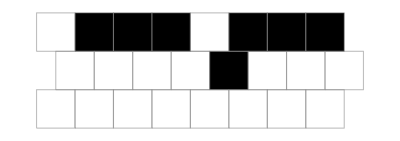
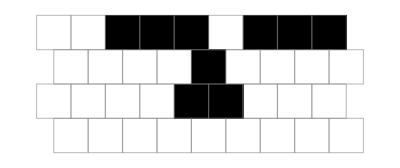
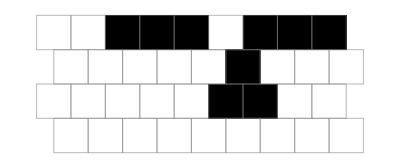
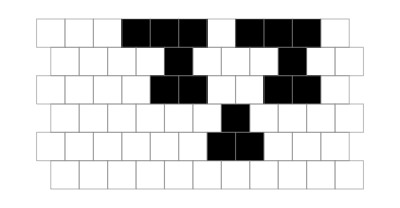
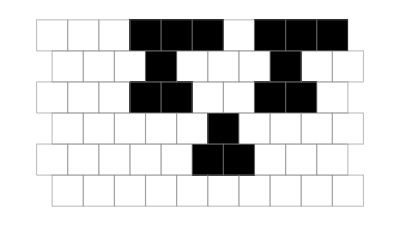
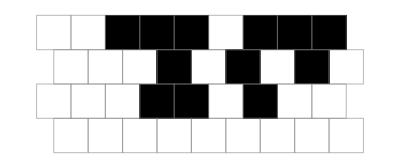
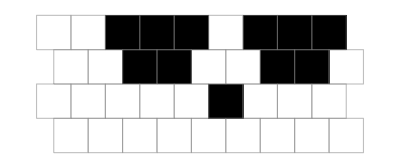
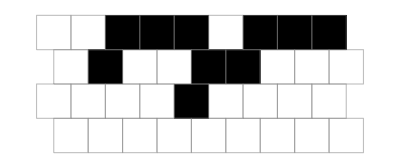

```mathematica
Module[{res,sublevels,vfs},
res=Reap[{{"[◼]", "EvolutionGraph"}}[2,3/2,
GraphLayout->"LayeredDigraphEmbedding"],
"SubLevels"];
sublevels=res[[2,1,1]];
res=res[[1]];
vfs=Association[KeyValueMap[Function[{key,rules},key->
{{"[◼]", "SerratedBricksArrayPlot"}}[#,ImageSize->{Automatic,(2+key[[1]])10}]
&@First[Union[CellularAutomaton[{#,2,3/2},{{1,1,1,0,1,1,1},0},
key[[1]]]&/@rules]]
],sublevels]];
Graph[res,
GraphLayout->"LayeredDigraphEmbedding",AspectRatio->2/3,
EdgeStyle->Gray,
VertexSize->1/2,
VertexShapeFunction->Function[
Inset[vfs[#2],#1,Automatic,
Times[#3[[1]],
#/Last[#]&@ImageDimensions[vfs[#2]],
Sqrt[First[#2]+5]
]
]
],
PerformanceGoal->"Quality"
]
]
```

And from this, interestingly, we can see our model’s version of discrete branches in the tree of life.

Zooming out further, we can look at this multiway graph (in the larger symmetric k = 2, r = 2 rule space), but instead of just one fitness-function, we can compare two different fitness functions:

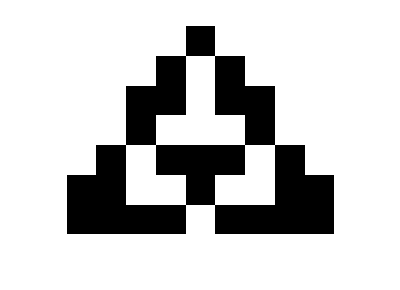
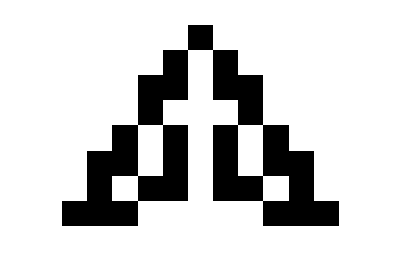
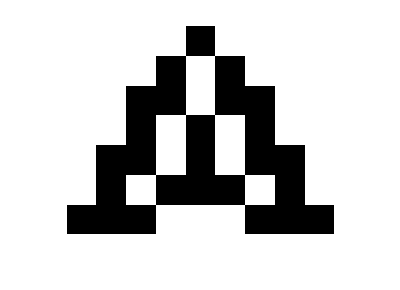
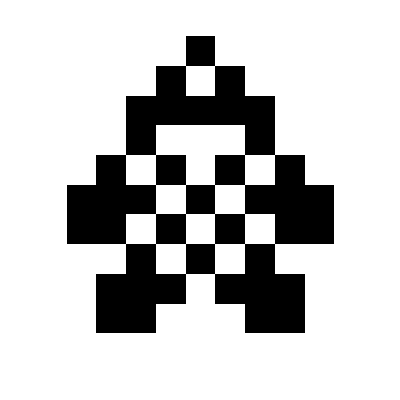
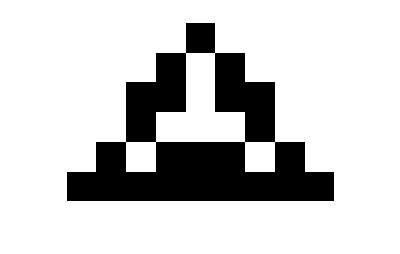
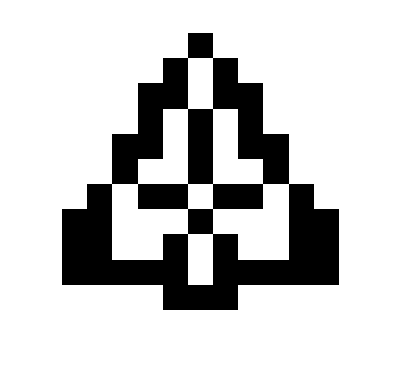
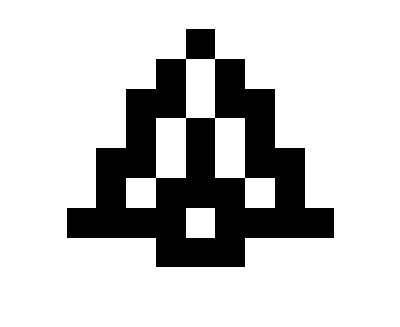
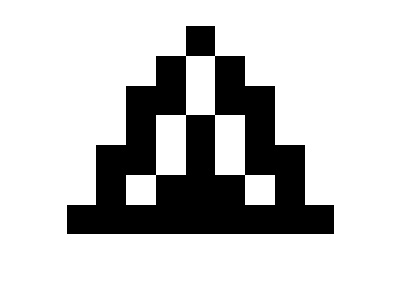

```mathematica
Module[{g1},
g1=VertexOutComponentGraph[{{"[◼]", "EvolutionaryMultiwayGraph"}}[{
{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],
{{"[◼]", "changeFitness"}}[{2,2},{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],
Length@*First]},
GraphLayout->"LayeredDigraphEmbedding",
"Reduced"->False,
AspectRatio->1,
EdgeStyle->{x_:>Association[
{1}->Directive[Hue[0.45, 0.54, 0.74],Thick,Opacity[8]],{2}->Directive[Hue[0.06, 0.96, 0.98],Thick,Opacity[8]],
{1,2}->Directive[{Hue[0.6,0.3,0.5,.35]}]
][Last[x]]}
],{{0,65815}}];
Legended[{{"[◼]", "addVertexFigures"}}[g1,{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],{2,2},
"VertexFigures"->1,VertexSize->1.2,AspectRatio->.7,ImageSize->550],LineLegend[{Directive[Hue[0.45, 0.54, 0.74],Thick,Opacity[8]],Directive[Hue[0.06, 0.96, 0.98],Thick,Opacity[8]],Directive[{Hue[0.6,0.5,0.5,.6]}]},{"height","width","both"}]]]
```

And so what we’re starting to see, is that we can view evolution as acting as a computationally bounded observer, selecting particular slices of the rule space. And Stephen then connects this idea to observers in physics, suggesting that much like there is the Second Law of Thermodynamics, there might also be similar high-level laws for the macroscopic “flow of evolution”.

### Future Directions

So now that we’ve told the Wolframian story of biology, and we’ve gotten a sense for the powerful foundations that have been laid down, you may be wondering, what does the future look like, where can we go from here?

As an indication of the strength of these foundations, Stephen has already made significant progress in applying these ideas to nearby fields.

For instance, he’s done extensive work on the connections between his recent model and machine learning. I won’t get into the details here, but one of the main takeaways is that the ways in which machine learning finds solutions are much like the way biology finds solutions, and therefore a lot of the claims around irreducibility also apply to machine learning models.

Another area that we’ve studied is medicine, and this is the project that I worked with him on. The key idea is to start with an adapted cellular automaton as models for an organism, then apply a perturbation to that automaton (indicated by the arrow):

```mathematica
Row[With[{ru={299459058088077823758143088095350287424,4,1},pt=<|{15,206}->0|>},{{{"[◼]", "PlotCA"}}[ru,"Steps"->24,ImageSize->{Automatic,200},Mesh->All,MeshStyle->Opacity[.1]],{{"[◼]", "PlotCA"}}[ru,"Steps"->105,ImageSize->{Automatic,450},Mesh->All,MeshStyle->Opacity[.1]],Spacer[20],{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{24,{-200,200}},pt],Mesh->All,MeshStyle->Opacity[.1],ImageSize->{Automatic,200}],{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{105,{-200,200}},pt],Mesh->All,MeshStyle->Opacity[.1],ImageSize->{Automatic,450}]}],Spacer[10],Alignment->Bottom]
```

-Graphics--Graphics--Graphics--Graphics-

So, we can then study the resulting changes to the pattern as a “metamodel for disease”:

```mathematica
With[{ru={299459058088077823758143088095350287424,4,1}},Row[Insert[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{120,{-200,200}},#],ImageSize->{Automatic,330}]&/@{<||>,<|{16,203}->0|>,<|{37,208}->3|>,<|{15,206}->0|>,<|{28,209}->2|>,<|{23,202}->3|>,<|{32,207}->0|>},Spacer[10],2],Spacer[1]]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

And the important point here is that, because of the irreducibility of the system, even a small change can have a large impact. In the two cases on the right, for example, a single-cell change, led to a very different pattern, with a very different lifetime. Further, because of irreducibility, predicting the changes to the system based on the nature of the perturbation will be computationally challenging.

And this brings us to the fundamental problem of medicine. Given that a perturbation has changed the behavior of the organism in a way that prevents it from achieving it’s goal, which we define here to be having for some finitely long lifetime, can we then “intervene” with a second perturbation, and bring the system back to a “healthy” state:

```mathematica
GraphicsRow[Insert[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1},{{1},0},{120,{-200,200}},#],ImageSize->{Automatic,220}]&/@{<|{23,202}->3|>,<|{23,202}->3,{57,214}->3|>,<|{23,202}->3,{44,209}->2|>,<|{23,202}->3,{34,208}->3|>,<|{23,202}->3,{26,204}->1|>,<|{23,202}->3,{31,202}->3|>,<|{23,202}->3,{35,207}->3|>,<|{23,202}->3,{52,211}->3|>,<||>},Spacer[25],{{2},{-2}}]]
```

-Graphics-

And what we find in general is that a lot of the previously vague, high-level phenomena of medicine, like the importance of early intervention for example, can be concretized in this model.

Going further, in studying the effects of perturbations on adapted systems, we are beginning to formalize when and where “pockets or reducibility” can be found. For instance, we can use a similar setup to the initial adaptive evolution, but instead of selecting purely for “lifetime”, we can select for lifetime under perturbation, as in:

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
SeedRandom[426778+132];
perts = Reap[bye = NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = {{"[◼]", "TestCALifeTime"}}[ca];
If[lt == -Infinity, #,
(*pcas = Table[PerturbCA[{ca, ru}], Ceiling[lt / 20]];*)
pcas = Table[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1}, 0},{200, {-200, 200}}],5];
Sow[{ru, pcas[[All, 2]]}];
fitness = Min[Join[{lt}, {{"[◼]", "TestCALifeTime"}}/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,4,1},0},2000]][[2, 1]];
```

```mathematica
kept = Select[perts, MemberQ[bye[[All, 1]],#[[1]]]&] ;
```

```mathematica
GraphicsRow[Function[{ru, perts}, With[{ca = {{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {28,  {-200, 200}}, #]},Labeled[{{"[◼]", "PlotCA"}}[ca, Mesh->True],Text[{{"[◼]", "TestCALifeTime"}}[ca]]]]&/@ Prepend[perts, <||>]]@@kept[[104]]]
```

-Graphics-

And the interesting finding, is that in subjecting our “computational organisms” to some noise in their environment, we start to select for more (not complete) reducibility in their mechanisms, here is one particularly reducible automaton that we found, that “uses” a big yellow blade to live a long lifetime despite changes in the environment:

```mathematica
rob = ;
reg = ;
(*See biomedicine-04 for definition*)
```

```mathematica
l1 = Select[rob, {{"[◼]", "TestCALifeTime"}}[CellularAutomaton[#[[1]], {{1}, 0}, 200]]>100&];
```

```mathematica
samplts = ;
```

```mathematica
zd = (samplts /. -Infinity->0);
```

```mathematica
bmi = With[{zd = (samplts /. -Infinity->0)}, 
ReverseSortBy[Range[Length[l1]],Mean[zd[[#]]]&]];
```

```mathematica
l1[[bmi[[1]],1]]
```

{297413941736400589979939780692294751544,4,1}

```mathematica
GraphicsRow[Table[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{297413941736400589979939780692294751544,4,1},{{1},0},{200,{-200,200}}],"ArrowSize"->Small], 10]]
```

-Graphics-

### Conclusion

But what does all this mean?

From following Stephen, and now working with him at the Wolfram Institute, I do believe that we’re having a bit of a “rule-30” moment. Just how before rule-30, there was no clear picture for the origin of complexity from simple systems, I think before Stephen’s recent work, there was no clear picture of an “idealized adaptive system”. And just like how that image of rule-30 eventually allowed Stephen to make broad unifications of various phenomena in different fields of science, I think we now have the potential to do something similar.

It is my hope that, in hearing this story, you can, like me, see this potential, and are as motivated as I am, to make this happen.

Thank you for reading.

### References

1. https://writings.stephenwolfram.com/2023/02/a-50-year-quest-my-personal-journey-with-the-second-law-of-thermodynamics/
2. https://writings.stephenwolfram.com/2011/10/the-background-and-vision-of-mathematica/
This video is an absolute gem, is a really good introduction to Mathematica, and is how I initially became obsessed with it:
https://www.youtube.com/watch?v=EjCWdsrVcBM 
3. https://www.wolframscience.com/nks/
4. https://www.wolframscience.com/nks/p383--fundamental-issues-in-biology/
5. https://writings.stephenwolfram.com/2024/03/can-ai-solve-science/#exploring-spaces-of-systems
6. https://writings.stephenwolfram.com/2024/05/why-does-biological-evolution-work-a-minimal-model-for-biological-evolution-and-other-adaptive-processes/#top
7. https://writings.stephenwolfram.com/2024/12/foundations-of-biological-evolution-more-results-more-surprises/#top
8. https://writings.stephenwolfram.com/2025/02/towards-a-computational-formalization-for-foundations-of-medicine/#top
9. https://www.wolframcloud.com/obj/wrn2001/Published/Draft-05-Cloud.nb